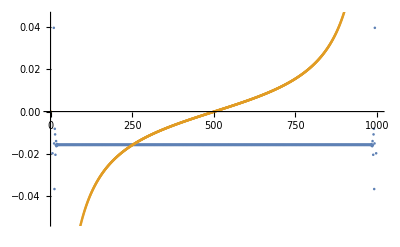

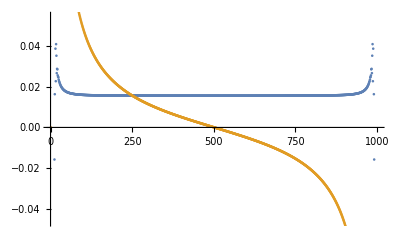

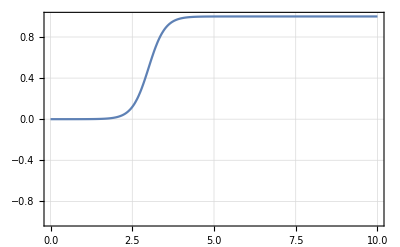

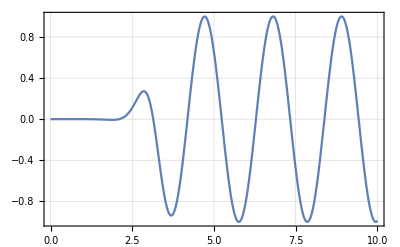

```mathematica
tanhLike[x_]:=(1 + Tanh[2 *(x - 3)])/2
sinLine[x_]:=tanhLike[x] * Sin[3 * x];

t = Table[tanhLike[10.0 * i / 1000.0],{i, 0, 1000}];
s = Table[sinLine[10.0 * i / 1000.0],{i, 0, 1000}];

fT = Fourier[t];
fS = Fourier[s];

ListPlot[{Re[fT],Im[fT]}]
ListPlot[{Re[fS],Im[fS]}]


(*
(*
cwdT=ContinuousWaveletTransform[t, GaborWavelet[6],{Automatic,16}]
cwdS=ContinuousWaveletTransform[s, GaborWavelet[6],{Automatic,16}]
*)

cwdT=ContinuousWaveletTransform[t]
cwdS=ContinuousWaveletTransform[s]

(*
ListLinePlot[cwdT[All,"Values"]]
ListLinePlot[cwdS[All,"Values"]]
*)

WaveletScalogram[cwdT,ColorFunction->"BlueGreenYellow"]
WaveletScalogram[cwdS,ColorFunction->"BlueGreenYellow"]

WaveletScalogram[cwdT,Automatic,Arg,ColorFunction->"BlueGreenYellow"]
WaveletScalogram[cwdS,Automatic,Arg,ColorFunction->"BlueGreenYellow"]
*)

Print[Plot[tanhLike[x], {x, 0, 10}, PlotRange -> {-1, 1}, Frame -> True, GridLines -> Automatic]];
Print[Plot[sinLine[x], {x, 0, 10}, PlotRange -> {-1, 1}, Frame -> True, GridLines -> Automatic]];

(* Plot[Re[FourierTransform[tanhLike[x], x, w]], {w, -10, 10}] *)
```